Autor: Artur Bednarczyk

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 6

Metoda sum skończonych

## Równanie Fredholma II rodzaju

### Zadanie

Metodą sum skończonych wyznaczyć rozwiązanie przybliżone równania:

y(x)=7/8 x-1/12+1/4∫_0^1 (x+t) y(t) ⅆt

Wykorzystać metodę trapezów.

Argument:  n

Wyznaczyć rozwiązanie dla n = 2, 4, 6, 8. 
Wykreślić błędy uzyskanych rozwiązań przybliżonych, gdy wiadomo, że rozwiązaniem dokładnym jest funkcja y(x)=x.

Wynik dla n = 2 : 1/570 (7+572 x)

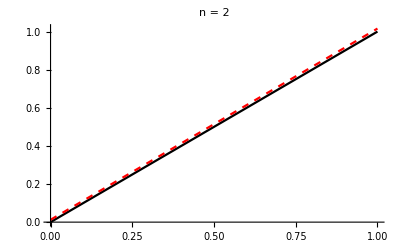

Błąd wynosi: 3/190

Wynik dla n = 4 : (7+2288 x)/2286

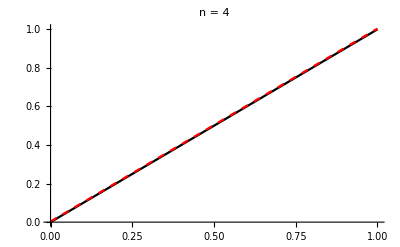

Błąd wynosi: 1/254

Wynik dla n = 6 : (7+5148 x)/5146

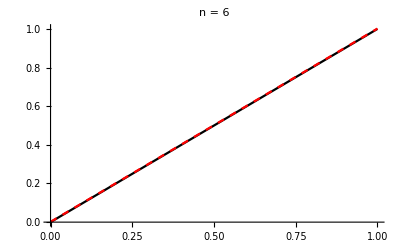

Błąd wynosi: 9/5146

Wynik dla n = 8 : (7+9152 x)/9150

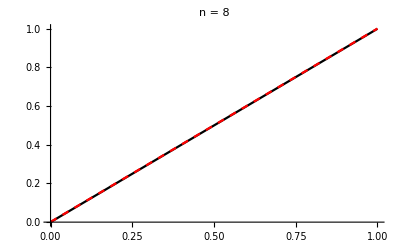

Błąd wynosi: 3/3050

```mathematica
(* Badana funkcja *)
func[x_]:= 7/8 x-1/12+1/4∫_0^1 (x+t)y[t]ⅆt;
k[x_, t_]:=x+t;
f[x_]:=7/8 x-1/12;
λ = 1/4;
a = 0;
b = 1;

(* Rozwiązanie *)
mss[f_, a_, b_, k_, λ_,n_ ]:=Module[{
results,
h = (b-a)/n,
A,
B,
X,
F,
y
},
A = Table[h, {i, 0, n}];
A⟦1⟧ = h/2;
A⟦n+1⟧ = h/2;
B = Table[0, {i,1,n+1}, {i, 1, n+1}];
X = Table[a + h*i, {i, 0, n}];
F = Table[f[X⟦i⟧],{i, 1, n+1}];

Do[
Do[
If[i ==j,
B⟦i⟧⟦j⟧ = 1 -λ*A⟦j⟧*k[X⟦i⟧, X⟦j⟧];,
B⟦i⟧⟦j⟧ = -λ*A⟦j⟧*k[X⟦i⟧, X⟦j⟧];
]
,{j, 1, n+1}];
,{i, 1, n+1}];
y = LinearSolve[B, F];
results = f[x]+λ*Sum[A⟦j⟧*(k[x,X⟦j⟧])*y⟦j⟧,{j,1,n+1}];
Return[Simplify[results]];
];
sPlot = Plot[x, {x, a,b}, PlotRange->All, PlotStyle->Black];
Do[
res = mss[f,a,b,k,λ, i];
Print["Wynik dla n = ", i, " : ", res];
rPlot = Plot[res, {x, a,b}, PlotRange->All, PlotStyle->{Red, Dashed}];
Print[Show[sPlot, rPlot, PlotLabel->StringForm["n = `1`",i ]]];
err = Abs[(res/.x->1) - 1];
Print["Błąd wynosi: ", err];
,{i,2,8,2}]
```